```mathematica
Clear["Global`*"]
```

## Constants

```mathematica
npart = 3;
nd = 2;
nbead=16;
beta=10;
nstep=200;
stepsize=(npart+1)/nstep;
dτ=beta/nbead*1.0;
ω=1;
m=1;
ℏ=1;
λ=ℏ^2/(2 m);
```

## Reference Beads

```mathematica
beads=Table[{RandomReal[{-npart,npart}],RandomReal[{-npart,npart}]},{i,1,npart}]
```

{{-2.22339,2.56035},{-2.04426,2.59281},{0.442342,-1.2197}}

```mathematica
refbead={{2.7,1.2}};
otherbeads={{-0.15,1.5},{-1.2,1.8}};
beads=Flatten[{refbead,otherbeads},1]
```

{{2.7,1.2},{-0.15,1.5},{-1.2,1.8}}

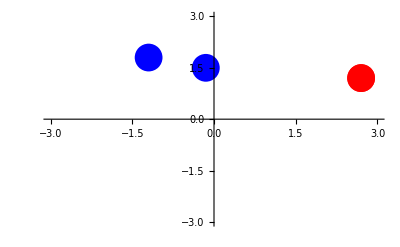

```mathematica
beadsPlot=ListPlot[{otherbeads,refbead},PlotStyle->{{PointSize[0.05],Blue},{PointSize[0.05],Red}},PlotRange-> {{-npart,npart},{-npart,npart}}]
```

```mathematica
allrefbeads=Table[{beads[[1,1]],beads[[1,2]],i},{i,1,nbead}];
allotherbeads=Flatten[Table[{beads[[j,1]],beads[[j,2]],i},{i,1,nbead},{j,2,npart}],1];
allbeadsPlot=ListPointPlot3D[{allotherbeads,allrefbeads},PlotStyle->{{PointSize[0.05],Blue},{PointSize[0.05],Red}},PlotRange-> {{-npart,npart},{-npart,npart},{0,nbead}}]
```

-Graphics3D-

## Nodal Plots

### Exact Nodes

```mathematica
rdotr[i_,j_,x_,y_]:=If[j==1,beads[[i]].{x,y},beads[[i]].beads[[j]]]
```

```mathematica
f[i_]:=ω/Sinh[i*dτ*ω]
ρij[i_,j_,k_,x_,y_]:=E^(f[k]rdotr[i,j,x,y])
ρ[x_,y_,k_]:=Table[ρij[i,j,k,x,y],{i,1,npart},{j,1,npart}]
```

```mathematica
ρ[x,y,k]
```

{{ⅇ^((2.7 x+1.2 y) Csch[0.625 k]),ⅇ^(1.395 Csch[0.625 k]),ⅇ^(-1.08 Csch[0.625 k])},{ⅇ^((-0.15 x+1.5 y) Csch[0.625 k]),ⅇ^(2.2725 Csch[0.625 k]),ⅇ^(2.88 Csch[0.625 k])},{ⅇ^((-1.2 x+1.8 y) Csch[0.625 k]),ⅇ^(2.88 Csch[0.625 k]),ⅇ^(4.68 Csch[0.625 k])}}

```mathematica
ρPlot=RegionPlot3D[Det[ρ[x,y,k]]> 0,{x,-npart,npart},{y,-npart,npart},{k,0.00001,nbead},PlotStyle->Directive[Opacity[0.90],LightBlue],MeshFunctions->{#3&},AxesLabel->{"x","y","β"},LabelStyle->{Bold,FontSize->15}];
Show[ρPlot,allbeadsPlot]
```

-Graphics3D-

### Ground State Nodes (Low T)

```mathematica
ϕ[n_,x_]:=((m ω)/(ℏ π))^(1/4)1/((2^n n!)^(1/2))E^(-m ω x^2/(2 ℏ))HermiteH[n,√((m ω)/ℏ)x]
ψ[n1_,n2_,x_,y_]:=ϕ[n1,x]ϕ[n2,y]
```

```mathematica
asdf[3]=Det[{{ψ[0,0,x,y],ψ[0,0,x1,y1],ψ[0,0,x2,y2]},{ψ[1,0,x,y],ψ[1,0,x1,y1],ψ[1,0,x2,y2]},{ψ[0,1,x,y],ψ[0,1,x1,y1],ψ[0,1,x2,y2]}}]/.{x1-> beads[[2,1]],y1-> beads[[2,2]],x2-> beads[[3,1]],y2-> beads[[3,2]]};
```

```mathematica
asdf[2]=((ψ[0,0,x,y]ψ[0,1,x1,y1]-ψ[0,0,x1,y1]ψ[0,1,x,y])+(ψ[0,0,x,y]ψ[1,0,x1,y1]-ψ[0,0,x1,y1]ψ[1,0,x,y]))/.{x1-> beads[[2,1]],y1-> beads[[2,2]]};
```

```mathematica
asdfa[2]=(ψ[0,0,x,y]ψ[0,1,x1,y1]-ψ[0,0,x1,y1]ψ[0,1,x,y])/.{x1-> beads[[2,1]],y1-> beads[[2,2]]};
```

```mathematica
asdfb[2]=(ψ[0,0,x,y]ψ[1,0,x1,y1]-ψ[0,0,x1,y1]ψ[1,0,x,y])/.{x1-> beads[[2,1]],y1-> beads[[2,2]]};
```

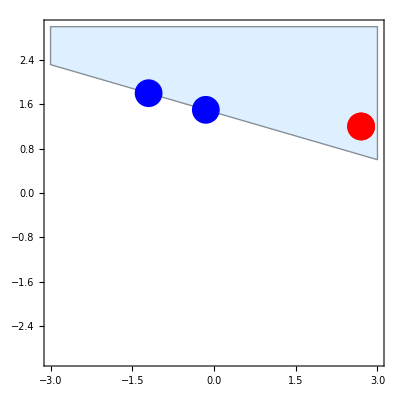

```mathematica
asdfPlot=RegionPlot[asdf[npart]< 0,{x,-npart,npart},{y,-npart,npart},PlotStyle-> LightBlue];
Show[asdfPlot,beadsPlot]
```

### Free Particle Nodes (High T)

```mathematica
rminusr[i_,j_,x_,y_]:=If[j==1,beads[[i]]-{x,y},beads[[i]]-beads[[j]]]
```

```mathematica
g[i_]:=-1/(4λ i dτ)
ρfij[i_,j_,k_,x_,y_]:=E^(g[k]rminusr[i,j,x,y].rminusr[i,j,x,y])
ρf[x_,y_,k_]:=Table[ρfij[i,j,k,x,y],{i,1,npart},{j,1,npart}]
```

```mathematica
ρfPlot=RegionPlot3D[Det[ρf[x,y,k]]≥ 0,{x,-npart,npart},{y,-npart,npart},{k,0.00001,nbead},PlotStyle->Directive[Opacity[0.90],LightBlue],MeshFunctions->{#3&},AxesLabel->{"x","y","β"},LabelStyle->{Bold,FontSize->15}];
Show[ρfPlot,allbeadsPlot]
```

-Graphics3D-